```mathematica
SetOptions[#,Axes->False,Frame->True]&/@{ListPlot,ListLinePlot,Plot,ListLogPlot};
SetDirectory["C:\\Users\\akandra\\Projects\\Kinetic Monte Carlo\\kmc\\data\\mmc"]
```

C:\Users\akandra\Projects\Kinetic Monte Carlo\kmc\data\mmc

## MMC

```mathematica
{TogglerBar[Dynamic[cfiles],FileNames["*.confs"],Appearance->"Vertical"],TogglerBar[Dynamic[efiles],FileNames["*.en"],Appearance->"Vertical"],TogglerBar[Dynamic[hfiles],FileNames["*.hist"],Appearance->"Vertical"]}
```

{






,






,


}

```mathematica
data=Import[#,"Table"]&/@cfiles;
{nlat,nads}=data[[All,1]]ᵀ
occs=Table[Partition[data[[i,2;;]],nlat[[i]]],{i,Length[data]}];
nframes=Length/@occs

energy=Import[#,"List"]&/@efiles;

data=Import[#,"Table"]&/@hfiles;
nhsteps=Flatten[data[[All,;;;;2]],{{3},{1,2}}];
hist=data[[All,2;;;;2]];
data=.
```

{{100,100},{2500,2500}}

{11,1001}

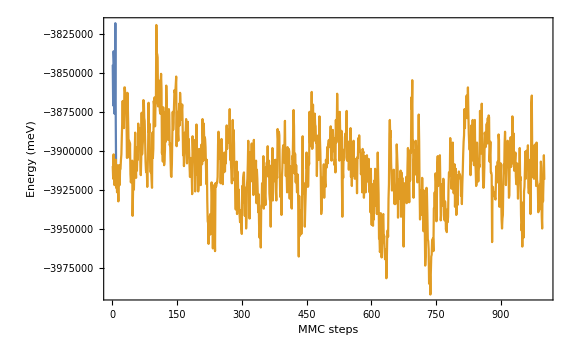

```mathematica
ListLinePlot[energy,PlotRange->All,FrameLabel->{"MMC steps","Energy (meV)"},ImageSize->Large]
```

```mathematica
size=Range[1,Length[#[[-1]]]]&/@hist;
```

```mathematica
(size[[1]] hist[[1,-1]])/nhsteps[[-1]]
```

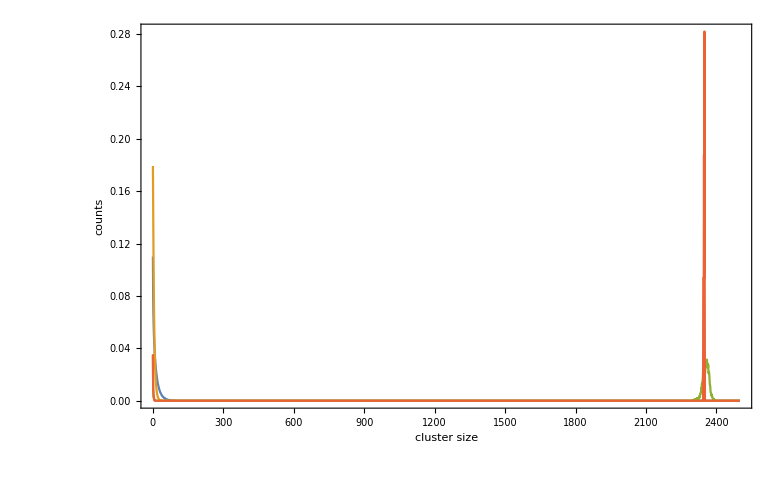

```mathematica
ListLinePlot[{(size hist[[-1]])/(nhsteps[[-1]]nads2),(size hist3[[-1]])/(nhsteps3[[-1]]nads3),(size hist5[[-1]])/(nhsteps5[[-1]]nads5),(size hist5[[1]])/(nhsteps5[[1]]nads5)},FrameLabel->{"cluster size","counts"},PlotRange->{All,All}]
```

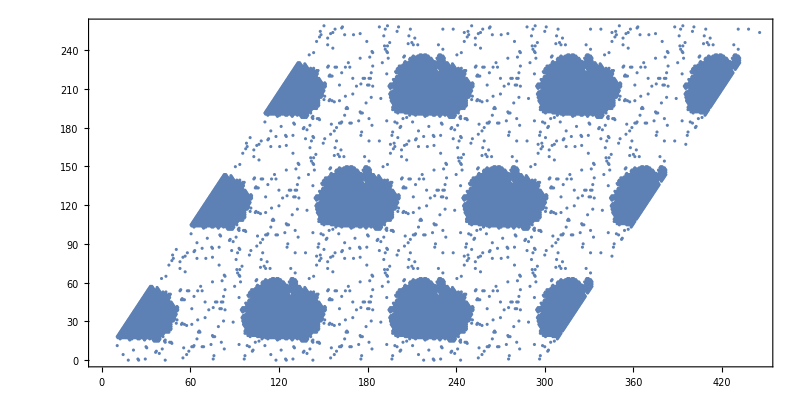

```mathematica
ListPlot[(((#-{1,1})&/@Position[ArrayPad[occs5[[-1]],nlat,"Periodic"],1]).{{1,0},{Cos[π/3],Sin[π/3]}}),AspectRatio->Cos[π/3]]
```

```mathematica
Manipulate[MatrixPlot[ArrayPad[occs5[[i]],nlat,"Periodic"],ColorFunction->"Monochrome"],{i,1,nframes,1}]
```

Part::partd: Part specification occs5⟦1⟧ is longer than depth of object.

ArrayPad::arr: First argument occs5⟦1⟧ to ArrayPad should be an array.

MatrixPlot::mat0: Argument occs5⟦1⟧ at position 1 is not a matrix.

```mathematica
Manipulate[MatrixPlot[ArrayPad[occs3[[i]],0,"Periodic"],ColorFunction->"Monochrome"],{i,1,nframes,1}]
```

## KMC

```mathematica
SetOptions[#,Axes->False,Frame->True]&/@{ListPlot,ListLinePlot,Plot,ListLogPlot};
SetDirectory["C:\\Users\\akandra\\Projects\\Kinetic Monte Carlo\\kmc\\data"]
```

C:\Users\akandra\Projects\Kinetic Monte Carlo\kmc\data

```mathematica
data=Import[#,"Table"]&/@FileNames["*.pos"];
{tend,nbins}=data[[1,1]];
Δr2=Table[Flatten[data[[i,2;;]]],{i,Length[data]}];
```

```mathematica
time=tend/nbins Table[i,{i,nbins}];
```

```mathematica
fit=LinearModelFit[{time,Mean[Δr2]}ᵀ,x,x]
```

FittedModel[-2.76852+20357.5 x]

```mathematica
Export["dr2_mean.dat",{time,Mean[Δr2]}ᵀ]
```

dr2_mean.dat

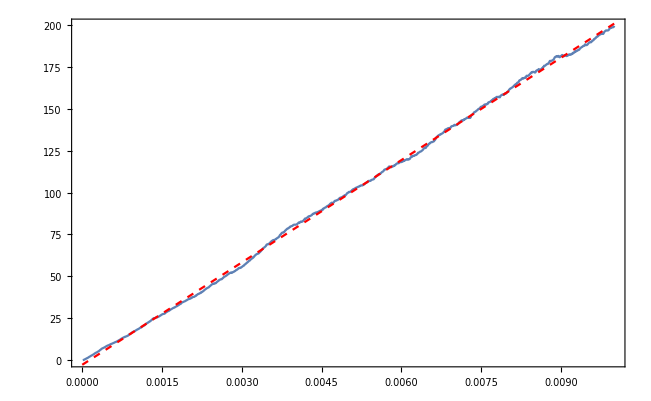

```mathematica
Show[ListLinePlot[{time,Mean[Δr2]}ᵀ],Plot[fit[x],{x,0,tend},PlotStyle->{Red,Dashed}]]
```

```mathematica
diff=fit["BestFitParameters"][[2]]/4
```

5089.37

```mathematica
5.0 10^9 Exp[-0.43 11604.52/400]
diff1=1^2/4%
```

19107.7

4776.92

```mathematica
diff/diff1
```

1.06541